```mathematica
T = Quantity[300, "Kelvins"];
kb = Quantity["BoltzmannConstant"];
A = Quantity[50, "Nanometers"];
cUp = Quantity[95, "Nanometers"];
P = Quantity[24, "Nanometers"];
omega0 = Quantity[1.85, 1 / "Nanometers"];
c= UnitConvert[kb * T * cUp * omega0^2, "Piconewtons"];
p = UnitConvert[kb * T * P * omega0^2, "Piconewtons"];
f = Quantity[1, "Piconewtons"];
g = UnitConvert[f - Sqrt[kb * T * f / A], "Piconewtons"];
cs = UnitConvert[c (1 - cUp / (4A) * Sqrt[kb * T / (A * f)]), "Piconewtons"];
tau0 = UnitConvert[Sqrt[2 * p * g / (omega0^2 * (1 - p / cs))], "Piconewtons" * "Nanometers"];
tauS =  UnitConvert[cs / omega0, "Piconewtons" * "Nanometers"];
tauP =  UnitConvert[p / omega0, "Piconewtons" * "Nanometers"];
sigmaS = 1 / cs * Sqrt[2 * p * g / (1 - p / cs)];
sigmaP = 1 / p * Sqrt[2 * p * g / (1 - p/cs)];
zRNAP=Quantity[4.42, "Nanometers"];
```

```mathematica
torque[sigma_]:=Piecewise[{{tauS*sigma,Abs[sigma] < Abs[sigmaS]},{tau0 * Sign[sigma] , Abs[sigmaS] ≤ Abs[sigma] ≤ Abs[sigmaP]},{tauP*sigma,Abs[sigmaP]≤ Abs[sigma]}}]
S[sigma_]:=Piecewise[{{-g+cs/2*sigma^2,Abs[sigma] < Abs[sigmaS]},{-g/(1-p/cs)+Sqrt[2p*g/(1-p/cs)]*Abs[sigma] , Abs[sigmaS] ≤ Abs[sigma] ≤ Abs[sigmaP]},{p/2*sigma^2,Abs[sigmaP]≤ Abs[sigma]}}]
bindingEnergy[sigma_]:=torque[sigma]*1.2*2Pi-zRNAP*S[sigma]
bindingEnergyNoBubble[sigma_]:=torque[sigma]*1.2*2Pi
```

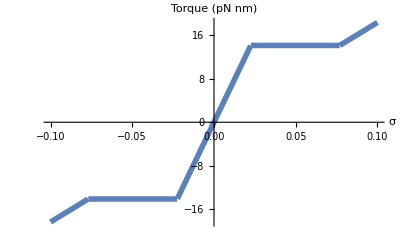

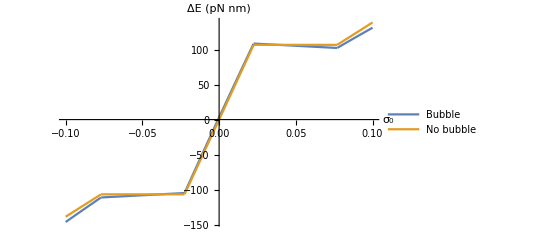

{{-307.394 nm pN,-277.318 nm pN},{-290.595 nm pN,-263.452 nm pN},{-273.948 nm pN,-249.587 nm pN},{-257.45 nm pN,-235.721 nm pN},{-241.103 nm pN,-221.855 nm pN},{-224.906 nm pN,-207.989 nm pN},{-208.86 nm pN,-194.123 nm pN},{-192.964 nm pN,-180.257 nm pN},{-177.218 nm pN,-166.391 nm pN},{-161.623 nm pN,-152.525 nm pN},{-146.178 nm pN,-138.659 nm pN},{-130.884 nm pN,-124.793 nm pN},{-115.739 nm pN,-110.927 nm pN},{-110.322 nm pN,-106.674 nm pN},{-109.165 nm pN,-106.674 nm pN},{-108.008 nm pN,-106.674 nm pN},{-106.852 nm pN,-106.674 nm pN},{-105.695 nm pN,-106.674 nm pN},{-92.6445 nm pN,-94.7646 nm pN},{-44.4914 nm pN,-47.3823 nm pN},{3.14785 nm pN,0. nm pN},{50.2732 nm pN,47.3823 nm pN},{96.8847 nm pN,94.7646 nm pN},{107.654 nm pN,106.674 nm pN},{106.497 nm pN,106.674 nm pN},{105.34 nm pN,106.674 nm pN},{104.183 nm pN,106.674 nm pN},{103.026 nm pN,106.674 nm pN},{106.115 nm pN,110.927 nm pN},{118.703 nm pN,124.793 nm pN},{131.14 nm pN,138.659 nm pN},{143.427 nm pN,152.525 nm pN},{155.564 nm pN,166.391 nm pN},{167.55 nm pN,180.257 nm pN},{179.386 nm pN,194.123 nm pN},{191.071 nm pN,207.989 nm pN},{202.606 nm pN,221.855 nm pN},{213.991 nm pN,235.721 nm pN},{225.225 nm pN,249.587 nm pN},{236.309 nm pN,263.452 nm pN},{247.243 nm pN,277.318 nm pN}}

```mathematica
Plot[torque[sigma],{sigma,-.1,.1},AxesLabel->{"σ","Torque (pN nm)"}, BaseStyle->{FontSize->16, FontFamily->"Helvetica Neue", FontColor->Black},PlotStyle->Thickness[.01]]
ePlot = Plot[{UnitConvert[bindingEnergy[sigma], "Piconewtons" * "Nanometers"],UnitConvert[bindingEnergyNoBubble[sigma], "Piconewtons" * "Nanometers"]},{sigma,-.1,.1},AxesLabel->{"σ_0","ΔE (pN nm)"},PlotLegends->{"Bubble","No bubble"}]
Table[UnitConvert[{sigma, bindingEnergy[sigma], bindingEnergyNoBubble[sigma]}, "Piconewtons" * "Nanometers"], {sigma,-0.2,0.2, 0.01}]
```